# Mathematica Plot Gallery

## Standard Plots

Function Plots

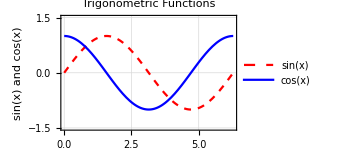

```mathematica
a=Plot[{Sin[x],Cos[x]},{x,0,2Pi},
		PlotStyle->{{Red,Dashed,Thick},{Blue,Thick}},
		PlotLabel->"Trigonometric Functions",
		Frame->True,
		FrameLabel->{"angle","sin(x) and cos(x)"},
		GridLines->Automatic,
		PlotRange->{{0,2Pi},{-1.5,1.5}},
		PlotLegends->{"sin(x)","cos(x)"},
		ImageSize->250]
```

```mathematica
GraphicsGrid[{{a,a},{a,a}}];
```

ListLinePlot

```mathematica
RandomVariate[NormalDistribution[0,1]]
```

0.641918

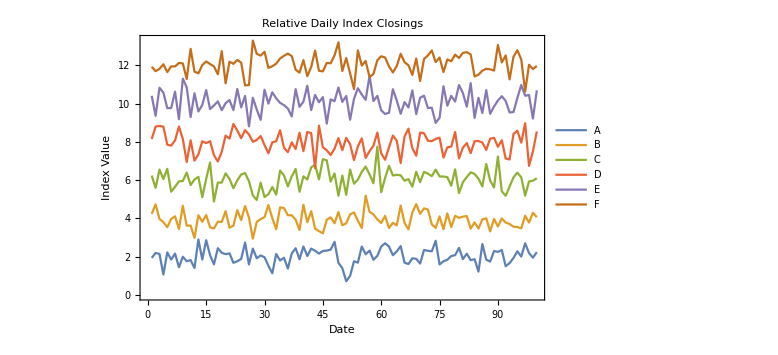

```mathematica
a= Block[{data},
	data=Table[Table[i+RandomVariate[NormalDistribution[i+0,0.5]],100],{i,6}];
	ListLinePlot[data,
		PlotLabel->"Relative Daily Index Closings",
		LabelStyle-> Directive[Bold, Purple],
		PlotLegends->Placed[{"A","B","C","D","E","F"},Right,Framed[#]&],
		Frame->True,
		FrameLabel->{"Date","Index Value"},
		ImageSize->Large]]
```

```mathematica
Labeled[a[[1]],a[[2,1]],Left];
```

ListPlot

```mathematica
Block[{data},
	data=Table[Table[i+RandomVariate[NormalDistribution[1,1]],100],{i,6}];
	ListPlot[data,
		PlotLabel->"Relative Daily Index Closings",
		PlotMarkers->{"❤",".b4∀`","(*.b4 `*)","◡̈⃝", "♡","꒰❃.b4◡`❃꒱"},
		LabelStyle-> Directive[Bold, Purple],
		PlotLegends->Placed[{"A","B","C","D","E","F"},Right,Framed[#]&],
		Frame->True,
		FrameLabel->{"Date","Index Value"},
		ImageSize->Large]]
```

-Graphics-

ContourPlot

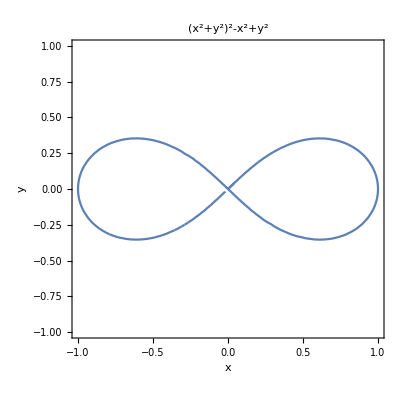

```mathematica
ContourPlot[(x^2+y^2)^2-x^2+y^2==0,{x,-1,1},{y,-1,1},
	PlotLabel->(x^2 + y^2)^2 - x^2 + y^2,
	Frame->True,
	FrameLabel->{"x","y"}]
```

```mathematica
FullForm[x^2]
```

Power[x,2]

```mathematica
Power[x,2]
```

x^2

PieChart

```mathematica
PieChart[{1,2,3,4,5},SectorOrigin->{Automatic,1},
		ChartLabels->{"a","b","c","d","(๑^ω^๑)"}]
```

-Graphics-

```mathematica
PieChart[{{1,2,3,4,5},{9,4,2,1,1}},ChartLabels->{"a","b","c","d","(๑^ω^๑)"}]
```

-Graphics-

```mathematica
PieChart[RandomReal[3,400],ChartStyle->"Rainbow",
		ChartBaseStyle->EdgeForm[None]]
```

-Graphics-

```mathematica
PieChart[{{1,1,1},{1,1,1},{1,1,1}}]
```

-Graphics-

```mathematica
PieChart[{{1,1,1,1},{1,1,1,1}}]
```

-Graphics-

```mathematica
FullForm[1]
```

Quantity[1,"Meters"]

```mathematica
Plot3D[Abs[Gamma[x+	I	y]],	{x,	-3,	3},	{y,	-2,	2}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u],	Sin[u]	+	Sin[u]^2*Cos[v],	Sin[v]},	{u,	
0,	2Pi},	{v,	-Pi,	Pi}]
```

-Graphics3D-

Line Plot 3D

```mathematica
Plot3D[{x^2+y^4-x^3+y^3},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t], Sin[t], Sin[5*t]}, {t, -Pi, Pi},
	PlotLabel->"x=cos(t),y=sin(t),z=sin(5t)",
	AxesLabel->{"x","y","z"},
	ViewPoint->{1.3, -2.4, 2.},
	PlotStyle->"Blue"]
```

-Graphics3D-

LogLogPlot

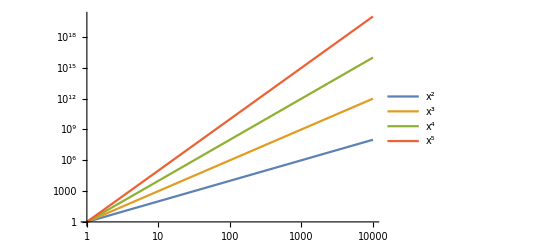

```mathematica
LogLogPlot[{x^2, x^3, x^4, x^5}, {x, 1, 10^4}, 
 PlotLegends -> "Expressions"]
```

```mathematica
zeta = {0.01 .02 0.05 0.1 .2 .5 1};
```

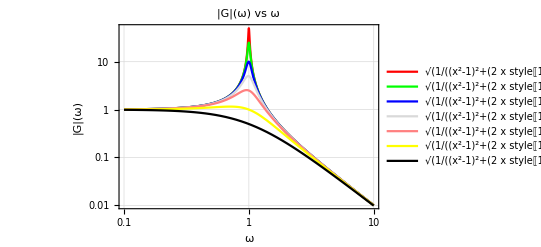

```mathematica
Show[Table[LogLogPlot[Sqrt[1/((x^2-1)^2+(2*x*style[[1]])^2)],{x,10^-1,10},
	PlotLabel->"|G|(ω) vs ω",
	PlotTheme->"Detailed",
	Frame->True,
	FrameLabel->{"ω","|G|(ω)"},
	PlotStyle->style[[2]]],{style,{{0.01,Red},
							{0.02,Green},
							{0.05,Blue},
							{0.1,LightGray},
							{0.2,Pink},
							{0.5,Yellow},
							{1,Black}}}]]
```

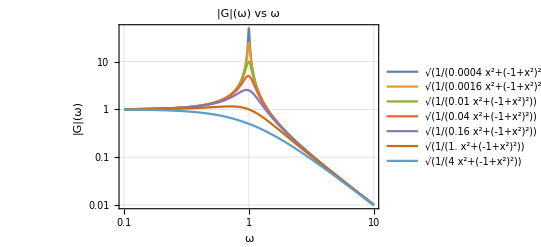

```mathematica
LogLogPlot[Evaluate[Table[Sqrt[1/((x^2-1)^2+(2*x*i)^2)],
	{i,{0.01,0.02,0.05,0.1,0.2,0.5,1}}]],{x,10^-1,10},
	PlotLabel->"|G|(ω) vs ω",
	PlotTheme->"Detailed",
	Frame->True,
	FrameLabel->{"ω","|G|(ω)"}]
```

## Customizing Plots

## Advanced Plots